```mathematica
(*The simulated bottleneck size value*)
```

```mathematica
Nb=3;
```

```mathematica
(*Total number of reads for the variant sites in the donor*)
```

```mathematica
varReadsDonor=Round[RandomVariate[NormalDistribution[500,100],500]];
```

```mathematica
(*discard anything below zero*)
```

```mathematica
varReadsDonor=Select[varReadsDonor,#>0 &];
```

```mathematica
(*Total number of reads for the variant sites in the recipient*)
```

```mathematica
varReadsRecipient=Round[RandomVariate[NormalDistribution[500,100],500]];
```

```mathematica
(*discard anything below zero*)
```

```mathematica
varReadsRecipient=Select[varReadsRecipient,#>0 &];
```

```mathematica
(*True variant frequencies in the donor*)
```

```mathematica
trueDonorFreq=RandomReal[{0.01,0.5},500];
```

```mathematica
(*frequencies below 1% are considered as noise and, therefore, are discarded*)
```

```mathematica
trueDonorFreq=Select[trueDonorFreq,#≥0.01 &];
```

```mathematica
(*any frequency above 50% is no longer a minor variant and should be discarded*)
```

```mathematica
trueDonorFreq=Select[trueDonorFreq,#<0.5 &];
```

```mathematica
(*number of reads for the variant in the donor*)
```

```mathematica
readsDonor={};
For[i=1,i≤Length[trueDonorFreq],i++,AppendTo[readsDonor,RandomVariate[BinomialDistribution[varReadsDonor⟦i⟧,trueDonorFreq⟦i⟧]]]]
```

```mathematica
(*observed frequency of the variants in the donor, i.e. variant reads / total reads*)
```

```mathematica
obsVarFreqD=N[readsDonor/varReadsDonor];
```

```mathematica
(*total number of variant reads in the founding population*)
```

```mathematica
variantsR={};
For[i=1,i≤Length[trueDonorFreq],i++,AppendTo[variantsR,RandomVariate[BinomialDistribution[Nb,trueDonorFreq⟦i⟧]]]]
```

```mathematica
(*see which variants did not make through the bottleneck, i.e. died out*)
```

```mathematica
temp=Flatten[Position[variantsR,0]]
```

{2,3,8,10,17,21,22,23,24,25,30,33,34,36,38,39,41,42,43,45,49,53,54,55,56,61,72,73,75,77,78,79,84,85,86,91,92,95,97,100,103,104,106,109,111,113,114,117,119,120,121,125,127,131,134,138,139,140,141,144,145,150,151,152,153,154,157,158,159,161,162,163,167,172,173,177,178,181,183,184,185,187,188,190,192,193,194,195,198,199,204,208,211,213,217,220,221,222,225,226,230,231,232,233,236,238,240,243,247,249,250,251,253,255,257,259,261,262,266,268,269,270,271,272,275,281,283,284,287,291,293,294,297,300,301,303,306,308,311,314,316,318,323,324,325,328,332,334,338,341,342,345,349,353,354,356,357,360,361,366,368,370,375,376,377,380,381,382,384,385,387,389,390,392,394,395,396,398,399,402,403,406,407,408,409,410,411,412,413,414,415,419,421,434,436,437,439,440,441,442,443,446,447,448,449,450,453,456,457,458,459,463,467,470,471,474,475,476,477,481,484,485,488,493,496,497,498,499}

```mathematica
(*true fraction of the viral population carrying the variant allele at the time of sampling*)
```

```mathematica
trueFractionCarrying={};
For[i=1,i≤Length[trueDonorFreq],i++,If[variantsR⟦i⟧==0,variantsR⟦i⟧=1];
AppendTo[trueFractionCarrying,RandomVariate[BetaDistribution[variantsR⟦i⟧,Nb-variantsR⟦i⟧]]]]
```

```mathematica
(*observed number of variant reads in the recipient*)
```

```mathematica
obsVarReadR={};
For[i=1,i≤Length[trueDonorFreq],i++,AppendTo[obsVarReadR,RandomVariate[BinomialDistribution[varReadsRecipient⟦i⟧,trueFractionCarrying⟦i⟧]]]]
```

```mathematica
(*observed frequency of the variant in the recipient*)
```

```mathematica
recipientFreq=N[obsVarReadR/varReadsRecipient];
```

```mathematica
(*there are some sites in the recipient for which the total reads are zero, we have to set their frequency back to zero*)
```

```mathematica
temp=Flatten[Position[variantsR,0]];
```

```mathematica
For[i=1,i++,i≤Length[temp],recipientFreq⟦temp⟦i⟧⟧=0]
```

```mathematica
Export["donorFreq.txt",obsVarFreqD]
```

donorFreq.txt

```mathematica
Export["recipientFreq.txt",recipientFreq]
```

recipientFreq.txt

```mathematica
(*estimate the bottleneck*)
```

```mathematica
likelihood1=ConstantArray[1,200];
For[i=1,i≤200,i++,
For[k=1,k≤Length[trueDonorFreq],k++,
likelihood1⟦i⟧*=PDF[NormalDistribution[obsVarFreqD⟦k⟧,Sqrt[(obsVarFreqD⟦k⟧(1-obsVarFreqD⟦k⟧)/(i))+((obsVarFreqD⟦k⟧*(1-obsVarFreqD⟦k⟧))/(1*i))]],recipientFreq⟦k⟧]]];
Flatten[Position[likelihood1,Max[likelihood1]]]
```

{43}

```mathematica
likelihood1=ConstantArray[1,200];
For[i=1,i≤200,i++,
For[k=1,k≤Length[trueDonorFreq],k++,
likelihood1⟦i⟧*=PDF[NormalDistribution[obsVarFreqD⟦k⟧,Sqrt[(obsVarFreqD⟦k⟧(1-obsVarFreqD⟦k⟧)/(i))]],recipientFreq⟦k⟧]]];
Flatten[Position[likelihood1,Max[likelihood1]]]
```

{21}

```mathematica
temp={3,44,56,109,127,198,227,235,283,308,375,379,471}
```

{3,44,56,109,127,198,227,235,283,308,375,379,471}

```mathematica
obsVarReadR[[44]]
```

160

```mathematica
bigTemp=Range[500];
```

```mathematica
temp
```

{22,26,36,44,50,55,60,67,77,78,92,95,98,102,107,129,131,139,145,160,165,167,170,178,185,194,202,203,209,219,225,241,248,249,251,265,266,276,283,296,300,305,307,315,319,320,325,346,349,353,355,358,363,370,388,395,398,413,417,419,420,428,448,450,451,454,459,460,470,477,480,484,493,500}

```mathematica
complmnt=Complement[bigTemp,temp]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,45,46,47,48,49,51,52,53,54,56,57,58,59,61,62,63,64,65,66,68,69,70,71,72,73,74,75,76,79,80,81,82,83,84,85,86,87,88,89,90,91,93,94,96,97,99,100,101,103,104,105,106,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,130,132,133,134,135,136,137,138,140,141,142,143,144,146,147,148,149,150,151,152,153,154,155,156,157,158,159,161,162,163,164,166,168,169,171,172,173,174,175,176,177,179,180,181,182,183,184,186,187,188,189,190,191,192,193,195,196,197,198,199,200,201,204,205,206,207,208,210,211,212,213,214,215,216,217,218,220,221,222,223,224,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,242,243,244,245,246,247,250,252,253,254,255,256,257,258,259,260,261,262,263,264,267,268,269,270,271,272,273,274,275,277,278,279,280,281,282,284,285,286,287,288,289,290,291,292,293,294,295,297,298,299,301,302,303,304,306,308,309,310,311,312,313,314,316,317,318,321,322,323,324,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,347,348,350,351,352,354,356,357,359,360,361,362,364,365,366,367,368,369,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,389,390,391,392,393,394,396,397,399,400,401,402,403,404,405,406,407,408,409,410,411,412,414,415,416,418,421,422,423,424,425,426,427,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,449,452,453,455,456,457,458,461,462,463,464,465,466,467,468,469,471,472,473,474,475,476,478,479,481,482,483,485,486,487,488,489,490,491,492,494,495,496,497,498,499}

```mathematica
likelihood1=ConstantArray[1,100];
For[p=1,p≤100,p++,
likelihood1⟦p⟧=∏_(i=1)^Length[temp] ∏_(j=1)^Length[complmnt] (1-obsVarFreqD⟦temp⟦i⟧⟧)^p(1-(1-obsVarFreqD⟦complmnt⟦j⟧⟧)^p)];
Flatten[Position[likelihood1,Max[likelihood1]]]
```

{9}

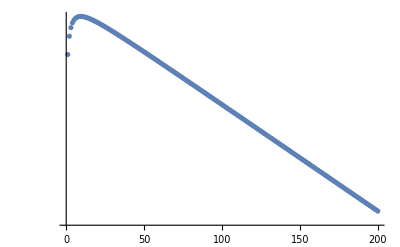

```mathematica
ListLogPlot[likelihood1]
```

```mathematica
likelihood1=ConstantArray[1,100];
For[bot=1,bot≤100,bot++,
For[p=1,p≤Length[obsVarFreqD],p++,
likelihood1⟦bot⟧*=∑_(m=0)^bot PDF[BinomialDistribution[bot,obsVarFreqD⟦p⟧],m]]];
Flatten[Position[likelihood1,Max[likelihood1]]]
```

$Aborted

{14}

```mathematica
val=1;
For[p=1,p≤Length[obsVarFreqD],p++,
Print[(∑_(m=0)^bot PDF[BinomialDistribution[varReadsRecipient,m/bot],obsVarReadR]*PDF[BinomialDistribution[bot,obsVarFreqD⟦p⟧],m])]]
```

$Aborted

```mathematica
val
```

1.

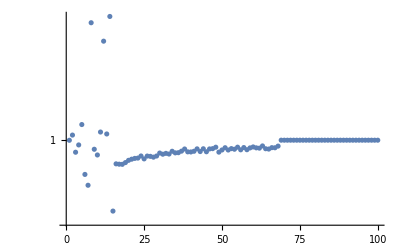

```mathematica
ListLogPlot[likelihood1]
```